```mathematica
Remove["Global`*"]
$HistoryLength=0;
ClearSystemCache[]
MemoryInUse[]

SetOptions[Plot,
PlotStyle->{{Red,Thick},{Purple,Thick},{Blue,Thick},{Cyan,Thick}},
Frame->True,
BaseStyle->{Medium,FontFamily->"Helvetica"},
ImageSize->600];
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

22503072

```mathematica
Zahl[α_]:=If[StringLength[ToString[α]]<3 || α≥10,StringJoin[ToString[α],"0"],ToString[α]];
Filename[type_,tau_,nst_,Nc_,cMax_]:=StringJoin["Result_",type,
"_tau",StringReplace[Zahl[tau],"."->"p"],
"_nst",ToString[nst],
"_Nc",ToString[Nc],
"_cMax",StringReplace[Zahl[cMax],"."->"p"],
".dat"];

Filename["BGKreduced",0.1,50,30,5.0]

ToNum[s_]:=Block[{Str,Erg},Str=StringToStream[s];Erg=Read[Str,Number];If[Erg==EndOfFile,Erg=0];Close[Str];Return[Erg];]
Expo[s_]:=If[s=="",StringInsert[s,"+00",1],If[ToNum[s]<-10,s,If[ToNum[s]<0,StringInsert[s,"0",2],If[ToNum[s]<10,StringInsert[s,"+0",1],StringInsert[s,"+",1]]]]];
MyFormat[a_]=NumberForm[a,{13,12},NumberFormat->(SequenceForm[#1,"E",Expo[#3]]&),ExponentFunction->(# &),NumberPadding->{"","0"},NumberSigns->{"-","+"}];

MyFormat[N[11234567890123456789,10]]
```

Result_BGKreduced_tau0p1_nst50_Nc30_cMax5p0.dat

+1.123456789000E+19

## BGK discretization (2 distributions, normal)

```mathematica
Clear[Maxwell,ρ,vx,vy,θ,fM0,fM,Nc,Nf,nn,cMax,dcx,dcy,cxPos,cyPos,fM$,cons,cons1,Maxwell,ffM]

fM[Cy_,ρ_,vx_,vy_,θ_]:={ρ+vy Cy+θ/2(Cy^2-1),2θ}1/(√(2π))Exp[-Cy^2/2];
proj[Cy_]:={{1,0},{Cy,0},{1/3(Cy^2-1),1/3},{2/3(Cy^2-1),-1/3},{Cy/2(Cy^2-3),Cy/2}};

ffM[ρ_,vx_,vy_,θ_]:=Maxwell.{ρ,vy,θ};

GetHalf[fin_,ii_]:=Take[Partition[fin,Nc]⟦Abs[ii]⟧,Sign[ii]Nc/2];

BoundaryDistribution[input_,side_,flag_]:=Block[{res,inL,inR},
Which[side=="L",
inL=Take[input,Nc/2];
res=Join[inL,GetHalf[ffM[ρL,0,0,θL],-flag]],
side=="R",
inR=Take[input,-Nc/2];
res=Join[GetHalf[ffM[ρR,0,0,θR],flag],inR]
];
res
];

BoundaryDistributionFull[input_,side_]:=Table[BoundaryDistribution[input⟦ii⟧,side,ii],{ii,1,Nf}]
```

```mathematica
Clear[n,dx,a,τ,uL,uR]
EqnP[n_,dx_,a_,τ_,uL_]:=Block[{ii,eqn1,eqn2,eqnN},
eqn1=a(uL-(u[1]+1/6(u[2]+3u[1]-4uL)))/dx-1/τ u[1];
eqn2=a(u[1]+1/6(u[2]+3u[1]-4uL)-(u[2]+1/4(u[3]-u[1])))/dx-1/τ u[2];
eqnN=a(u[n-1]+1/4(u[n]-u[n-2])-(u[n]+1/2(u[n]-u[n-1])))/dx-1/τ u[n];
Join[{eqn1,eqn2},
Table[a(u[i-1]+1/4(u[i]-u[i-2])-(u[i]+1/4(u[i+1]-u[i-1])))/dx-1/τ u[i],{i,3,n-1}],
{eqnN}]

];
EqnM[n_,dx_,a_,τ_,uR_]:=Block[{ii,eqnN,eqnN1,eqn1},
eqnN=a(u[n]-1/6(-u[n-1]-3u[n]+4uR)-uR)/dx-1/τ u[n];
eqnN1=a(u[n-1]-1/4(u[n]-u[n-2])-(u[n]-1/6(-u[n-1]-3u[n]+4uR)))/dx-1/τ u[n-1];
eqn1=a(u[1]-1/2(u[2]-u[1])-(u[2]-1/4(u[3]-u[1])))/dx-1/τ u[1];
Join[{eqn1},
Table[a(u[i]-1/4(u[i+1]-u[i-1])-(u[i+1]-1/4(u[i+2]-u[i])))/dx-1/τ u[i],{i,2,n-2}],
{eqnN1,eqnN}]

];
```

```mathematica
Clear[ρ,vx,vy,θ]
Clear[aP,aM,uR,uL,u,a]

nn=300;
Δx=1./nn;

Nf=2;
Nc=150;
cMax=5.;
dcy=2 cMax/(Nc-1);
cyPos=Table[-cMax+(j-1)dcy,{j,1,Nc}];


fM$={
Flatten[Transpose[Table[fM[cyPos⟦m⟧,1,0,0,0],{m,1,Nc}]]],
Flatten[Transpose[Table[fM[cyPos⟦m⟧,0,0,1,0],{m,1,Nc}]]],
Flatten[Transpose[Table[fM[cyPos⟦m⟧,0,0,0,1],{m,1,Nc}]]]};

cons=Normal[CoefficientArrays[Sum[proj[cyPos⟦j⟧].Table[u[j,ii],{ii,1,Nf}],{j,1,Nc}]dcy,Flatten[Table[Table[u[m,ii],{m,1,Nc}],{ii,1,Nf}]]]⟦2⟧];

Maxwell=Transpose[fM$]+Transpose[cons].Inverse[Normal[cons.Transpose[cons]]].(IdentityMatrix[5]⟦All,1;;3⟧-cons.Transpose[fM$]);

P=Maxwell.cons⟦1;;3⟧;

time=AbsoluteTiming[ (* direct initialization using compressed format !! *)
PP=SparseArray[Automatic,{nn Nf Nc,nn Nf Nc},0,{1,
{Table[i Nf Nc,{i,0,nn Nf Nc}],
Flatten[Table[Table[{i Nf Nc+m2},{m1,1,Nf Nc},{m2,1,Nf Nc}],{i,0,nn-1}],2]},
Flatten[Table[P,{i,1,nn}]]
}]
]⟦1⟧;
Print[" collision part - time: ",time];


{bcP,AdvP}=CoefficientArrays[EqnP[nn,Δx,aP,∞,uL],Table[u[i],{i,1,nn}]];
{bcM,AdvM}=CoefficientArrays[EqnM[nn,Δx,aM,∞,uR],Table[u[i],{i,1,nn}]];

time=AbsoluteTiming[
A=CoefficientArrays[Flatten[Transpose[Flatten[Table[{
Transpose[AdvM.Table[u[i,jj],{i,1,nn}]/.{aM u[i_,ii_]->Table[cyPos⟦m⟧u[i,m,ii],{m,1,Nc/2}]}],
Transpose[AdvP.Table[u[i,jj],{i,1,nn}]/.{aP u[i_,ii_]->Table[cyPos⟦m⟧u[i,m,ii],{m,Nc/2+1,Nc}]}]}
,{jj,1,Nf}],2]]]
,Flatten[Table[u[i,m,ii],{i,1,nn},{ii,1,Nf},{m,1,Nc}]]]⟦2⟧
]⟦1⟧;
Print[" advection part - time: ",time];


bc=Flatten[Table[Flatten[Table[{bcM⟦i⟧/.{uR->uR[ii]},bcP⟦i⟧/.{uL->uL[ii]}},{ii,1,Nf}]],{i,1,nn}]];

Do[
If[Length[bc⟦i⟧]==0,bc⟦i⟧=Table[0,{m,1,Nc/2}]]
,{i,1,Length[bc]}]

bc=bc/.{aP uL[ii_]->aP.uL[ii],aM uR[ii_]->aM.uR[ii]};
bc=bc/.{aP->DiagonalMatrix[Table[cyPos⟦m⟧,{m,Nc/2+1,Nc}]],aM->DiagonalMatrix[Table[cyPos⟦m⟧,{m,1,Nc/2}]]};
bc=Flatten[bc/.{uL[ii_]:>GetHalf[ffM[ρL,0,0,θL],-ii],uR[ii_]:>GetHalf[ffM[ρR,0,0,θR],ii]}];
```

collision part - time: 37.16958

advection part - time: 3.82501

## Simple Heat Conduction

```mathematica
SetDirectory["/home/torrilhon/Documents/RWTH/Projects/KineticReference/BGKSimpleHeat"]
SetDirectory["C:/Users/mt/Science/Projekte/KineticReference/BGKSimpleHeat"]
```

/home/torrilhon/Documents/RWTH/Projects/KineticReference/SimpleHeat

SetDirectory::cdir: Cannot set current directory to "C:/Users/mt/Science/Projekte/KineticReference/SimpleHeat".

$Failed

### Kn = 0.1

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
{nr,Nc,nn,rho}
{1,50,100,0.8844739274418416}
{2,100,200,0.8845409868058839}
{3,150,300,0.8845526137056255}
{3,200,400,0.8845566736276641}
{4,300,600,0.8845596346942822}
```

```mathematica
nr=1;

tau=0.1;
rho[nr]=0.8845526137056255;
setup={ρL->-rho[nr],ρR->rho[nr],θL->1.0,θR->-1.0};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]];
xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

{rho[nr],Total[uN⟦All,3⟧]}

ρN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
vyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
θN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
σyyN[nr]=Interpolation[uN⟦All,{1,5}⟧,InterpolationOrder->1];
qyN[nr]=Interpolation[uN⟦All,{1,6}⟧,InterpolationOrder->1];
```

{0.884553,-3.73921×10^-13}

```mathematica
p1={0.8845596346942822,-0.0008093014469847069};
p2={0.9,-4.220879835234518};
p1⟦1⟧-p1⟦2⟧(p2⟦1⟧-p1⟦1⟧)/(p2⟦2⟧-p1⟦2⟧)
```

0.884557

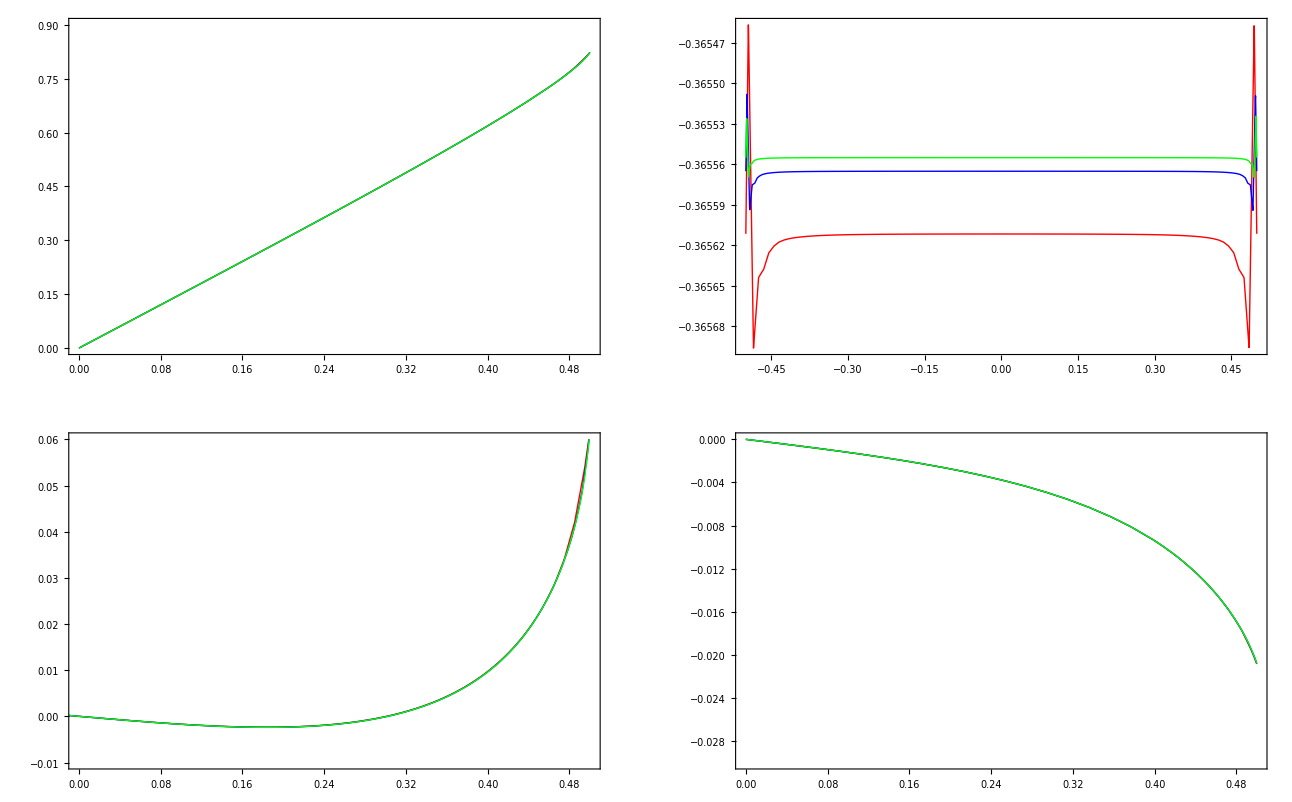

```mathematica
show={1,2,3};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
θNSF[x_]=1.5228482041791787 x;

GraphicsGrid[{
{Plot[Evaluate[Map[θN[#][-x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.9}},PlotStyle->style],
Plot[Evaluate[Map[-qyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.3,-0.4}},PlotStyle->style]},
{Plot[Evaluate[Map[θN[#][-x]-θNSF[x]&,show]],{x,xa,xe},PlotRange->{{0.0,0.5},{-0.01,0.06}},PlotStyle->style],
Plot[Evaluate[Map[σyyN[#][-x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.03,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,ρN[nr][##],vyN[nr][##],θN[nr][##],ρN[nr][##]+θN[nr][##],σyyN[nr][##],qyN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p1_nst300_Nc150_cMax5p0.dat,67451]

### Kn = 0.3

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
{nr,Nc,nn,rho}
{3,150,300,0.7733242447819767}
{4,200,400,0.7733331591472816}
{5,300,600,0.7733395224605312}
```

```mathematica
nr=1;

tau=0.3;
rho[nr]=0.7733242447819767;
setup={ρL->-rho[nr],ρR->rho[nr],θL->1.0,θR->-1.0};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]];
xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

{rho[nr],Total[uN⟦All,3⟧]}

ρN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
vyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
θN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
σyyN[nr]=Interpolation[uN⟦All,{1,5}⟧,InterpolationOrder->1];
qyN[nr]=Interpolation[uN⟦All,{1,6}⟧,InterpolationOrder->1];
```

{0.773324,-1.47585×10^-13}

```mathematica
p1={0.7733331591472816,-0.0018836157487319934};
p2={0.8,-5.636618078701297};
p1⟦1⟧-p1⟦2⟧(p2⟦1⟧-p1⟦1⟧)/(p2⟦2⟧-p1⟦2⟧)
```

0.773324

```mathematica
show={1,2,3};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
θNSF[x_]=1.5228482041791787 x;

GraphicsGrid[{
{Plot[Evaluate[Map[θN[#][-x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.9}},PlotStyle->style],
Plot[Evaluate[Map[-qyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.3,-0.4}},PlotStyle->style]},
{Plot[Evaluate[Map[θN[#][-x]-θNSF[x]&,show]],{x,xa,xe},PlotRange->{{0.0,0.5},{-0.01,0.06}},PlotStyle->style],
Plot[Evaluate[Map[σyyN[#][-x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.03,0.0}},PlotStyle->style]}}]
```

-Graphics-

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,ρN[nr][##],vyN[nr][##],θN[nr][##],ρN[nr][##]+θN[nr][##],σyyN[nr][##],qyN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p3_nst300_Nc150_cMax5p0.dat,75904]

### Kn = 0.5

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
{nr,Nc,nn,rho}
{1,50,100,0.7167315516703209}
{2,100,200,0.716940805766147}
{3,150,300,0.7169763562169682}
{4,200,400,0.7169885143164658}
{5,300,600,0.716997138540253}
```

```mathematica
nr=2;

tau=0.5;
rho[nr]=0.7169763562169682;
setup={ρL->-rho[nr],ρR->rho[nr],θL->1.0,θR->-1.0};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]];
xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

{rho[nr],Total[uN⟦All,3⟧]}

ρN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
vyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
θN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
σyyN[nr]=Interpolation[uN⟦All,{1,5}⟧,InterpolationOrder->1];
qyN[nr]=Interpolation[uN⟦All,{1,6}⟧,InterpolationOrder->1];
```

{0.716976,1.41762×10^-14}

```mathematica
p1={0.716997138540253,-0.002471764613331713};
p2={0.7,4.869030483993683};
p1⟦1⟧-p1⟦2⟧(p2⟦1⟧-p1⟦1⟧)/(p2⟦2⟧-p1⟦2⟧)
```

0.716989

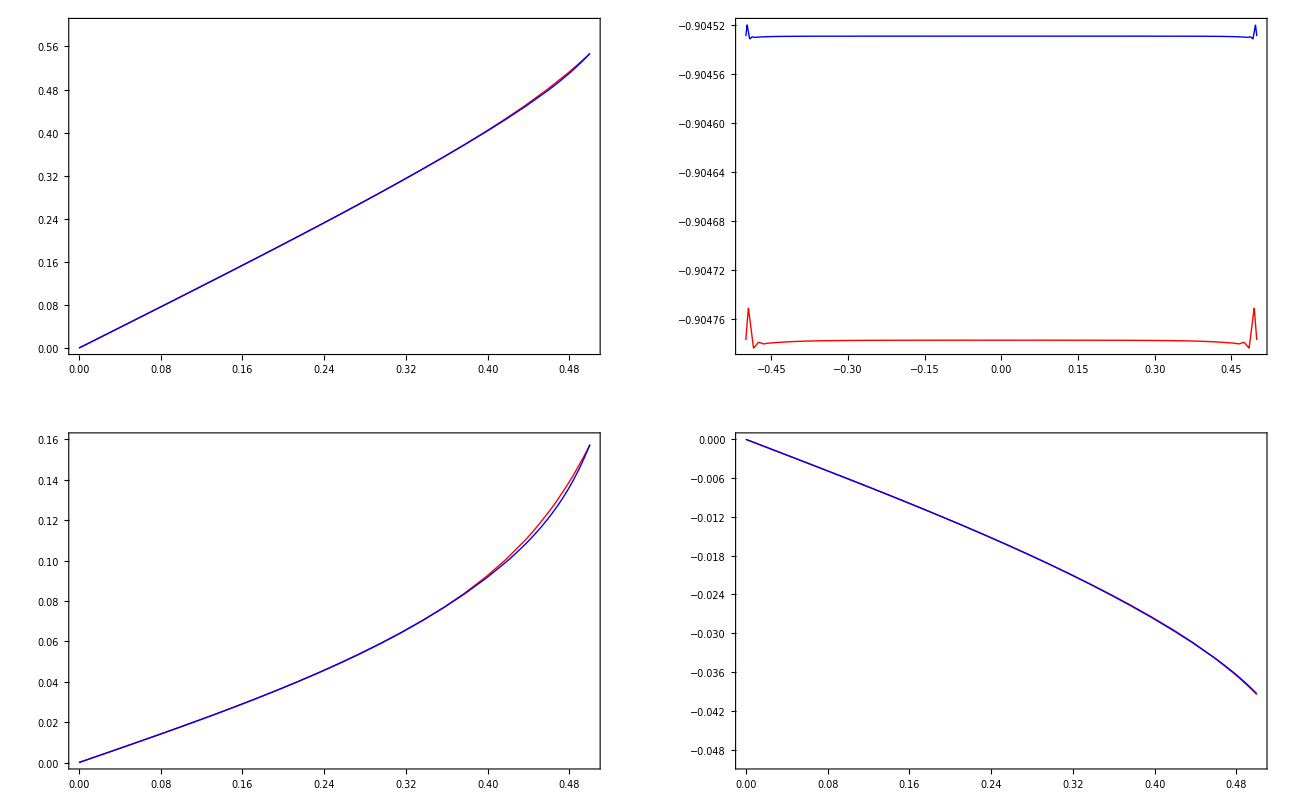

```mathematica
show={1,2};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
θNSF[x_]=0.7792280639979607 x;

GraphicsGrid[{
{Plot[Evaluate[Map[θN[#][-x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.6}},PlotStyle->style],
Plot[Evaluate[Map[-qyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.9,-0.95}},PlotStyle->style]},
{Plot[Evaluate[Map[θN[#][-x]-θNSF[x]&,show]],{x,xa,xe},PlotRange->{{0.0,0.5},{-0.0,0.16}},PlotStyle->style],
Plot[Evaluate[Map[σyyN[#][-x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.05,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,ρN[nr][##],vyN[nr][##],θN[nr][##],ρN[nr][##]+θN[nr][##],σyyN[nr][##],qyN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p5_nst300_Nc150_cMax5p0.dat,84357]

## Poiseuille Heat Conduction

```mathematica
SetDirectory["/home/torrilhon/Documents/RWTH/Projects/KineticReference/BGKPoiseuilleHeat"]
SetDirectory["C:/Users/mt/Science/Projekte/KineticReference/BGKPoiseuilleHeat"]
```

/home/torrilhon/Documents/RWTH/Projects/KineticReference/PoiseuilleHeat

SetDirectory::cdir: Cannot set current directory to "C:/Users/mt/Science/Projekte/KineticReference/PoiseuilleHeat".

$Failed

### Kn = 0.1

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
nr=5;

tau=0.1;

rhs=Flatten[Table[(-0.5+Δx/2+(i-1)Δx)^2 2/3 ffM[0,0,0,1],{i,1,nn}]];

setup={ρL->0,ρR->0,θL->0.0,θR->0.0};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];

time=AbsoluteTiming[
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]-rhs];
]⟦1⟧;
Print["system size: ",nn Nf Nc," linear solve - time: ",time];

xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

{Total[uN⟦All,3⟧]}

ρN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
vyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
θN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
σyyN[nr]=Interpolation[uN⟦All,{1,5}⟧,InterpolationOrder->1];
qyN[nr]=Interpolation[uN⟦All,{1,6}⟧,InterpolationOrder->1];
```

system size: 90000 linear solve - time: 59.8233

{-6.93129×10^-15}

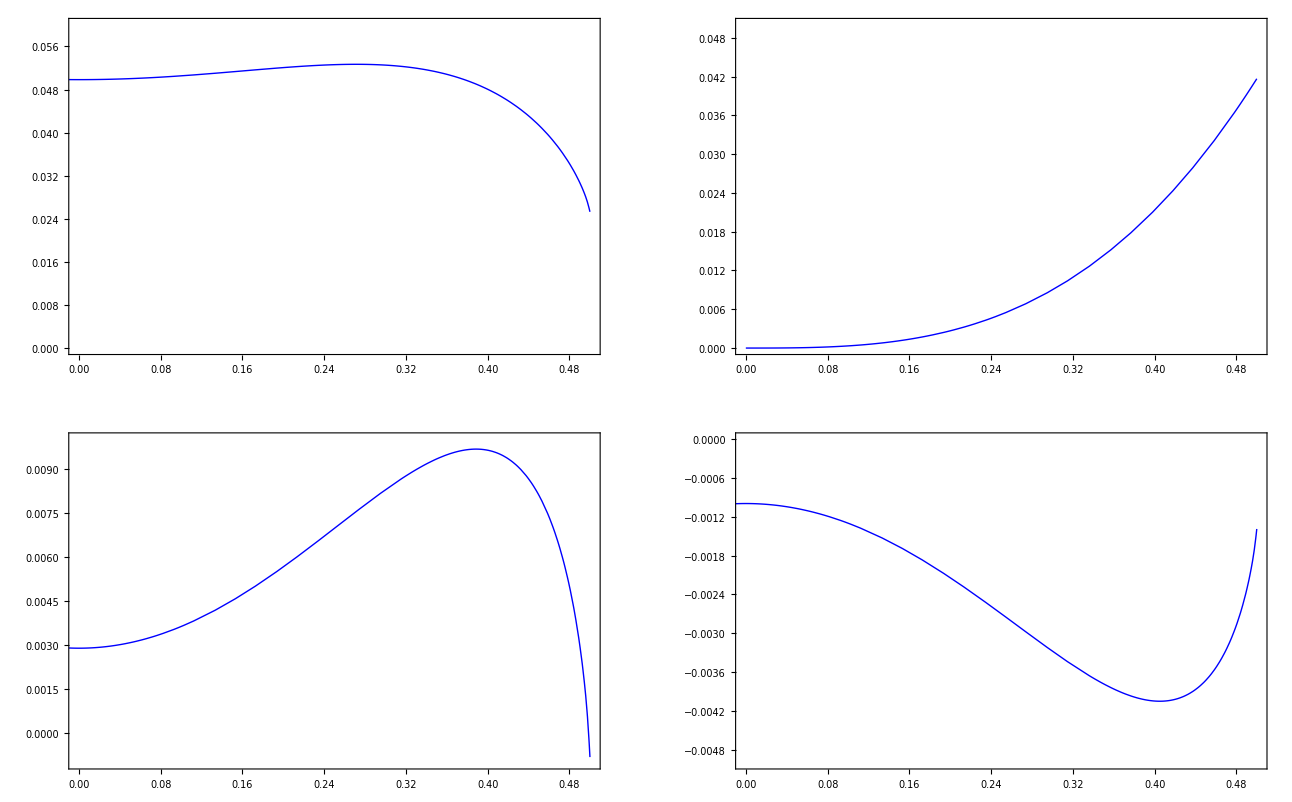

```mathematica
show={4,5};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
θNSF[x_]=-√(2/3) (-1.2822393491689084+0.408248290463863 x^4)-1;

GraphicsGrid[{
{Plot[Evaluate[Map[θN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.06}},PlotStyle->style],
Plot[Evaluate[Map[qyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.05}},PlotStyle->style]},
{Plot[Evaluate[Map[θN[#][x]-θNSF[x]&,show]],{x,xa,xe},PlotRange->{{0.0,0.5},{-0.001,0.01}},PlotStyle->style],
Plot[Evaluate[Map[σyyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.005,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,ρN[nr][##],vyN[nr][##],θN[nr][##],ρN[nr][##]+θN[nr][##],σyyN[nr][##],qyN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p1_nst300_Nc150_cMax5p0.dat,92808]

### Kn = 0.3

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
nr=5;

tau=0.3;

rhs=Flatten[Table[(-0.5+Δx/2+(i-1)Δx)^2 2/3 ffM[0,0,0,1],{i,1,nn}]];

setup={ρL->0,ρR->0,θL->0.0,θR->0.0};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];

time=AbsoluteTiming[
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]-rhs];
]⟦1⟧;
Print[" linear solve - time: ",time];

xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

{Total[uN⟦All,3⟧]}

ρN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
vyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
θN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
σyyN[nr]=Interpolation[uN⟦All,{1,5}⟧,InterpolationOrder->1];
qyN[nr]=Interpolation[uN⟦All,{1,6}⟧,InterpolationOrder->1];
```

linear solve - time: 57.22841

{9.39099×10^-15}

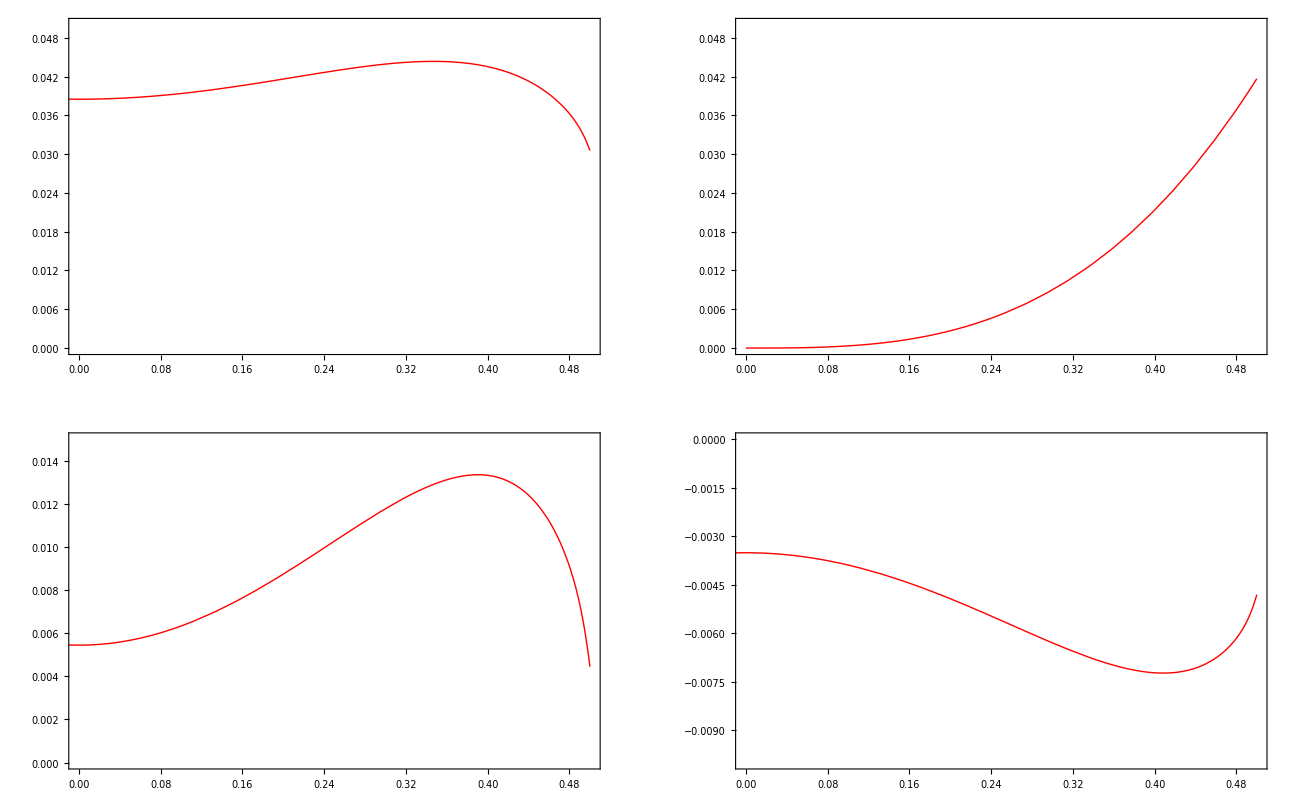

```mathematica
show={4};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
θNSF[x_]=-√(2/3) (-1.2652290037329141+0.13608276348795437 x^4)-1;

GraphicsGrid[{
{Plot[Evaluate[Map[θN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.05}},PlotStyle->style],
Plot[Evaluate[Map[qyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.05}},PlotStyle->style]},
{Plot[Evaluate[Map[θN[#][x]-θNSF[x]&,show]],{x,xa,xe},PlotRange->{{0.0,0.5},{-0.0,0.015}},PlotStyle->style],
Plot[Evaluate[Map[σyyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.01,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,ρN[nr][##],vyN[nr][##],θN[nr][##],ρN[nr][##]+θN[nr][##],σyyN[nr][##],qyN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p3_nst300_Nc150_cMax5p0.dat,101253]

### Kn = 0.5

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
nr=5;

tau=0.5;

rhs=Flatten[Table[(-0.5+Δx/2+(i-1)Δx)^2 2/3 ffM[0,0,0,1],{i,1,nn}]];

setup={ρL->0,ρR->0,θL->0.0,θR->0.0};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];

time=AbsoluteTiming[
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]-rhs];
]⟦1⟧;
Print[" linear solve - time: ",time];

xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

{Total[uN⟦All,3⟧]}

ρN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
vyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
θN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
σyyN[nr]=Interpolation[uN⟦All,{1,5}⟧,InterpolationOrder->1];
qyN[nr]=Interpolation[uN⟦All,{1,6}⟧,InterpolationOrder->1];
```

linear solve - time: 52.23315

{-3.08005×10^-16}

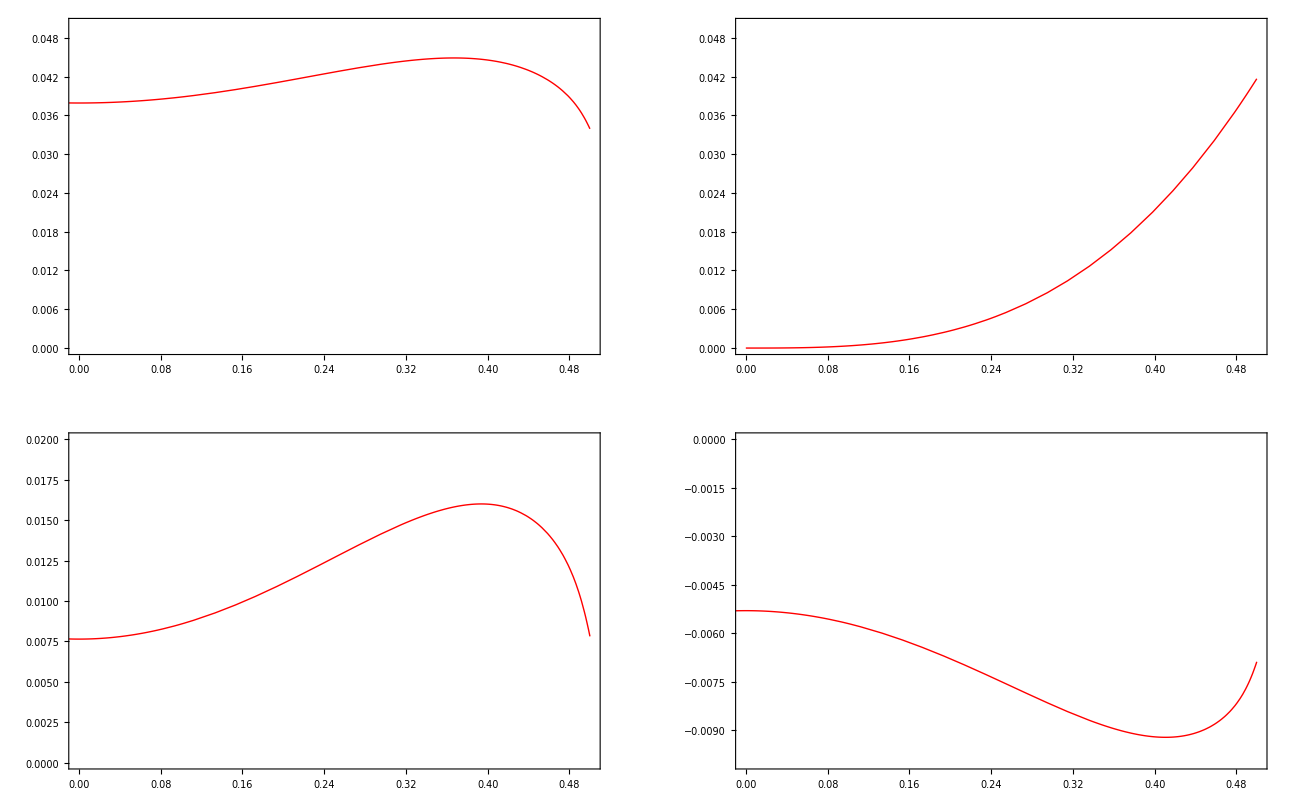

```mathematica
show={4};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
θNSF[x_]=-√(2/3) (-1.2618269346457154+0.08164965809277261 x^4)-1;

GraphicsGrid[{
{Plot[Evaluate[Map[θN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.05}},PlotStyle->style],
Plot[Evaluate[Map[qyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.05}},PlotStyle->style]},
{Plot[Evaluate[Map[θN[#][x]-θNSF[x]&,show]],{x,xa,xe},PlotRange->{{0.0,0.5},{-0.0,0.02}},PlotStyle->style],
Plot[Evaluate[Map[σyyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.01,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,ρN[nr][##],vyN[nr][##],θN[nr][##],ρN[nr][##]+θN[nr][##],σyyN[nr][##],qyN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p5_nst300_Nc150_cMax5p0.dat,109690]

## BGK discretization (1 distribution, tangential)

```mathematica
Clear[Maxwell,ρ,vx,vy,θ,fM0,fM,Nc,Nf,nn,cMax,dcx,dcy,cxPos,cyPos,fM$,cons,cons1,Maxwell,ffM]

fM[Cy_,ρ_,vx_,vy_,θ_]:={vx}1/(√(2π))Exp[-Cy^2/2];
proj[Cy_]:={{1},{Cy},{1/2(Cy^2-1)}};

ffM[ρ_,vx_,vy_,θ_]:=Maxwell.{vx};

GetHalf[fin_,ii_]:=Take[Partition[fin,Nc]⟦Abs[ii]⟧,Sign[ii]Nc/2];

BoundaryDistribution[input_,side_,flag_]:=Block[{res,inL,inR},
Which[side=="L",
inL=Take[input,Nc/2];
res=Join[inL,GetHalf[ffM[0,vWL,0,0],-flag]],
side=="R",
inR=Take[input,-Nc/2];
res=Join[GetHalf[ffM[0,vWR,0,0],flag],inR]
];
res
];

BoundaryDistributionFull[input_,side_]:=Table[BoundaryDistribution[input⟦ii⟧,side,ii],{ii,1,Nf}]
```

```mathematica
Clear[n,dx,a,τ,uL,uR]
EqnP[n_,dx_,a_,τ_,uL_]:=Block[{ii,eqn1,eqn2,eqnN},
eqn1=a(uL-(u[1]+1/6(u[2]+3u[1]-4uL)))/dx-1/τ u[1];
eqn2=a(u[1]+1/6(u[2]+3u[1]-4uL)-(u[2]+1/4(u[3]-u[1])))/dx-1/τ u[2];
eqnN=a(u[n-1]+1/4(u[n]-u[n-2])-(u[n]+1/2(u[n]-u[n-1])))/dx-1/τ u[n];
Join[{eqn1,eqn2},
Table[a(u[i-1]+1/4(u[i]-u[i-2])-(u[i]+1/4(u[i+1]-u[i-1])))/dx-1/τ u[i],{i,3,n-1}],
{eqnN}]

];
EqnM[n_,dx_,a_,τ_,uR_]:=Block[{ii,eqnN,eqnN1,eqn1},
eqnN=a(u[n]-1/6(-u[n-1]-3u[n]+4uR)-uR)/dx-1/τ u[n];
eqnN1=a(u[n-1]-1/4(u[n]-u[n-2])-(u[n]-1/6(-u[n-1]-3u[n]+4uR)))/dx-1/τ u[n-1];
eqn1=a(u[1]-1/2(u[2]-u[1])-(u[2]-1/4(u[3]-u[1])))/dx-1/τ u[1];
Join[{eqn1},
Table[a(u[i]-1/4(u[i+1]-u[i-1])-(u[i+1]-1/4(u[i+2]-u[i])))/dx-1/τ u[i],{i,2,n-2}],
{eqnN1,eqnN}]

];
```

```mathematica
Clear[ρ,vx,vy,θ]
Clear[aP,aM,uR,uL,u,a]

nn=300;
Δx=1./nn;

Nf=1;
Nc=150;
cMax=5.;
dcy=2 cMax/(Nc-1);
cyPos=Table[-cMax+(j-1)dcy,{j,1,Nc}];


fM$={
Flatten[Transpose[Table[fM[cyPos⟦m⟧,0,1,0,0],{m,1,Nc}]]]
};

cons=Normal[CoefficientArrays[Sum[proj[cyPos⟦j⟧].Table[u[j,ii],{ii,1,Nf}],{j,1,Nc}]dcy,Flatten[Table[Table[u[m,ii],{m,1,Nc}],{ii,1,Nf}]]]⟦2⟧];

Maxwell=Transpose[fM$]+Transpose[cons].Inverse[Normal[cons.Transpose[cons]]].(IdentityMatrix[3]⟦All,1;;1⟧-cons.Transpose[fM$]);

P=Maxwell.cons⟦1;;1⟧;

time=AbsoluteTiming[ (* direct initialization using compressed format !! *)
PP=SparseArray[Automatic,{nn Nf Nc,nn Nf Nc},0,{1,
{Table[i Nf Nc,{i,0,nn Nf Nc}],
Flatten[Table[Table[{i Nf Nc+m2},{m1,1,Nf Nc},{m2,1,Nf Nc}],{i,0,nn-1}],2]},
Flatten[Table[P,{i,1,nn}]]
}]
]⟦1⟧;
Print[" collision part - time: ",time];


{bcP,AdvP}=CoefficientArrays[EqnP[nn,Δx,aP,∞,uL],Table[u[i],{i,1,nn}]];
{bcM,AdvM}=CoefficientArrays[EqnM[nn,Δx,aM,∞,uR],Table[u[i],{i,1,nn}]];

time=AbsoluteTiming[
A=CoefficientArrays[Flatten[Transpose[Flatten[Table[{
Transpose[AdvM.Table[u[i,jj],{i,1,nn}]/.{aM u[i_,ii_]->Table[cyPos⟦m⟧u[i,m,ii],{m,1,Nc/2}]}],
Transpose[AdvP.Table[u[i,jj],{i,1,nn}]/.{aP u[i_,ii_]->Table[cyPos⟦m⟧u[i,m,ii],{m,Nc/2+1,Nc}]}]}
,{jj,1,Nf}],2]]]
,Flatten[Table[u[i,m,ii],{i,1,nn},{ii,1,Nf},{m,1,Nc}]]]⟦2⟧
]⟦1⟧;
Print[" advection part - time: ",time];


bc=Flatten[Table[Flatten[Table[{bcM⟦i⟧/.{uR->uR[ii]},bcP⟦i⟧/.{uL->uL[ii]}},{ii,1,Nf}]],{i,1,nn}]];

Do[
If[Length[bc⟦i⟧]==0,bc⟦i⟧=Table[0,{m,1,Nc/2}]]
,{i,1,Length[bc]}]

bc=bc/.{aP uL[ii_]->aP.uL[ii],aM uR[ii_]->aM.uR[ii]};
bc=bc/.{aP->DiagonalMatrix[Table[cyPos⟦m⟧,{m,Nc/2+1,Nc}]],aM->DiagonalMatrix[Table[cyPos⟦m⟧,{m,1,Nc/2}]]};
bc=Flatten[bc/.{uL[ii_]:>GetHalf[ffM[0,vWL,0,0],-ii],uR[ii_]:>GetHalf[ffM[0,vWR,0,0],ii]}];
```

collision part - time: 8.89898

advection part - time: 1.91169

## Planar Couette Flow

```mathematica
SetDirectory["/home/torrilhon/Documents/RWTH/Projects/KineticReference/BGKCouetteFlow"]
SetDirectory["C:/Users/mt/Science/Projekte/KineticReference/BGKCouetteFlow"]
```

/home/torrilhon/Documents/RWTH/Projects/KineticReference/BGKCouetteFlow

SetDirectory::cdir: Cannot set current directory to "C:/Users/mt/Science/Projekte/KineticReference/BGKCouetteFlow".

$Failed

### Kn = 0.1

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
nr=1;

tau=0.1;
setup={vWL->-1.0/2,vWR->1.0/2};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
time=AbsoluteTiming[
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]];
]⟦1⟧;
Print["system size: ",nn Nf Nc," linear solve - time: ",time];

xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

vxN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
σxyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
qxN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
```

system size: 45000 linear solve - time: 5.99121

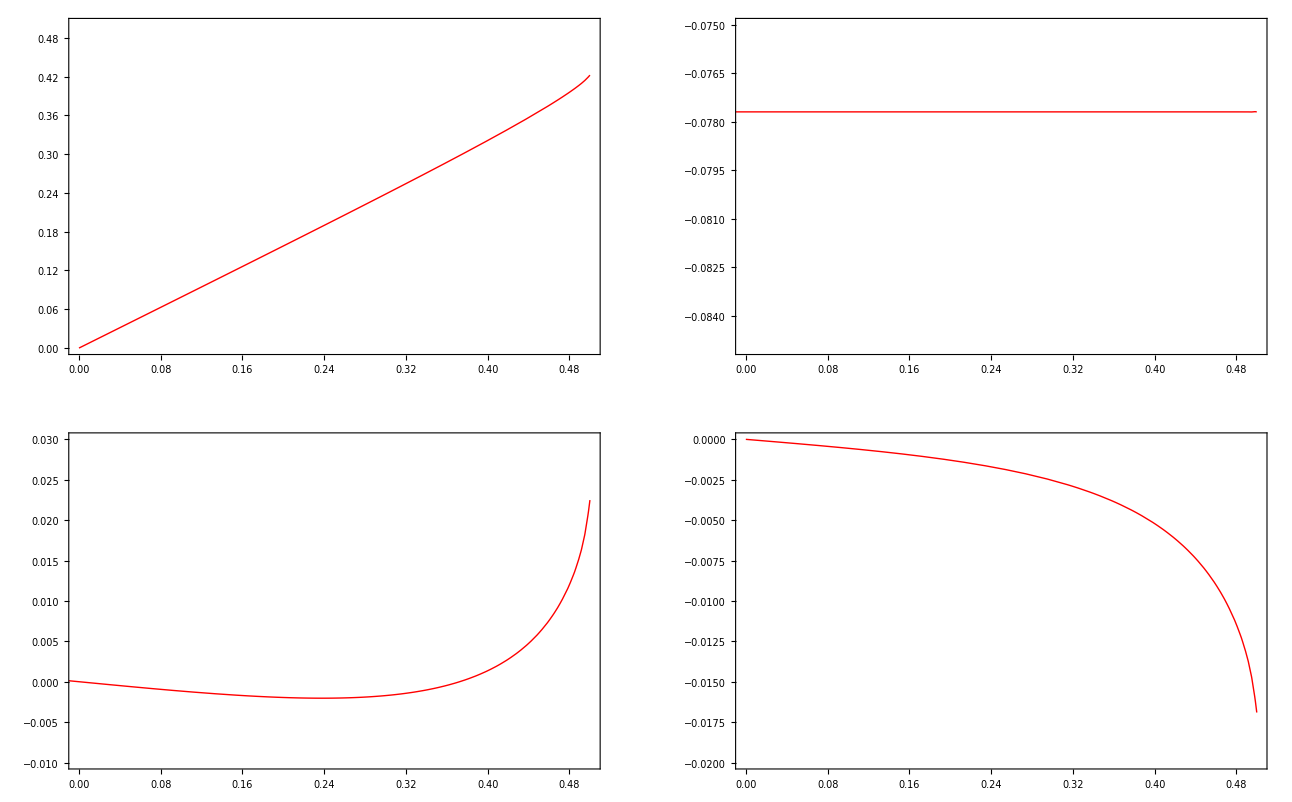

```mathematica
show={1,2,3};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
vxNSF[x_]=0.7995760152466068 x;

GraphicsGrid[{{
Plot[Evaluate[Map[vxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.5}},PlotStyle->style],
Plot[Evaluate[Map[σxyN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.085,-0.075}},PlotStyle->style]},
{Plot[Evaluate[Map[vxN[#][x]-vxNSF[x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.01,0.03}},PlotStyle->style],Plot[Evaluate[Map[qxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.02,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,vxN[nr][##],σxyN[nr][##],qxN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p1_nst300_Nc150_cMax5p0.dat,101247]

### Kn = 0.3

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
nr=1;

tau=0.3;
setup={vWL->-1.0/2,vWR->1.0/2};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
time=AbsoluteTiming[
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]];
]⟦1⟧;
Print["system size: ",nn Nf Nc," linear solve - time: ",time];

xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

vxN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
σxyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
qxN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
```

system size: 45000 linear solve - time: 6.15988

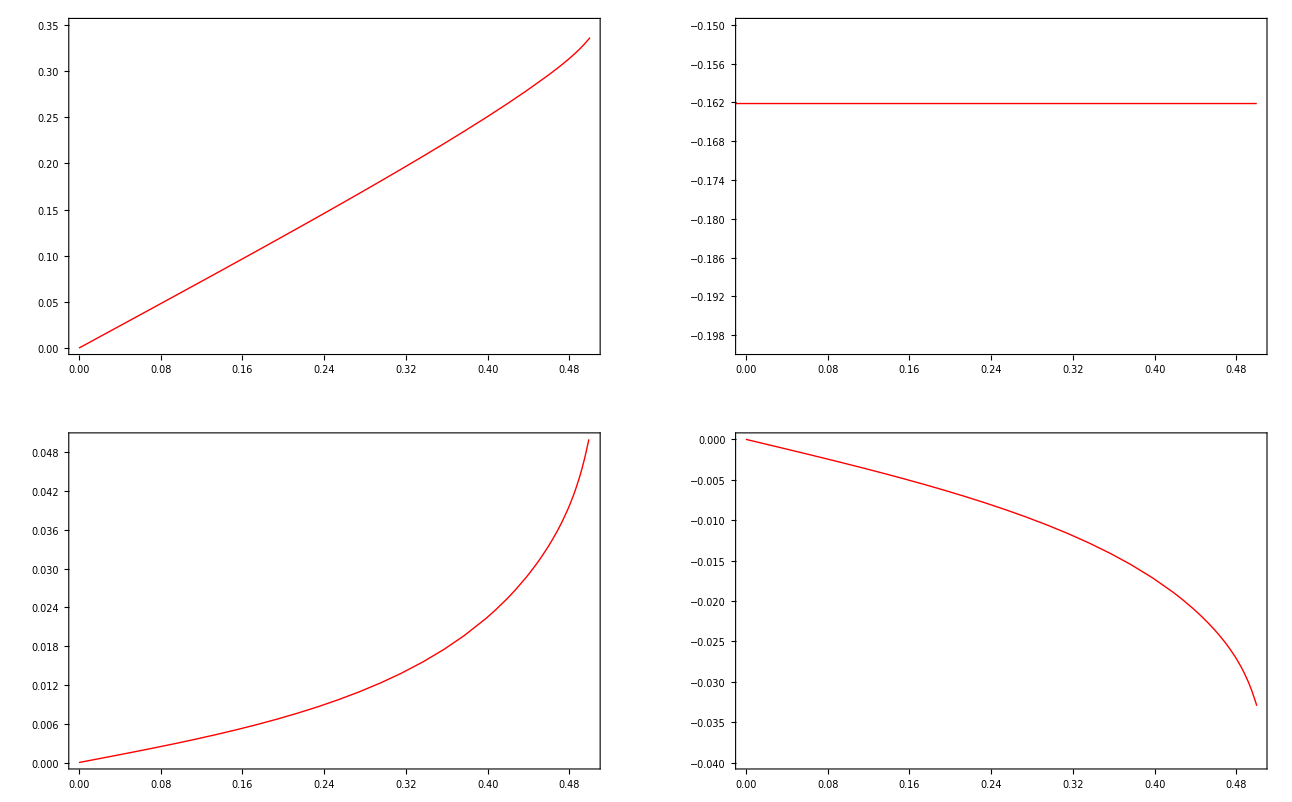

```mathematica
show={1,2,3};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
vxNSF[x_]=0.5707800080033832 x;

GraphicsGrid[{{
Plot[Evaluate[Map[vxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.35}},PlotStyle->style],
Plot[Evaluate[Map[σxyN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.2,-0.15}},PlotStyle->style]},
{Plot[Evaluate[Map[vxN[#][x]-vxNSF[x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.0,0.05}},PlotStyle->style],Plot[Evaluate[Map[qxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.04,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,vxN[nr][##],σxyN[nr][##],qxN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p3_nst300_Nc150_cMax5p0.dat,106080]

### Kn = 0.5

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
nr=5;

tau=0.5;
setup={vWL->-1.0/2,vWR->1.0/2};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
time=AbsoluteTiming[
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]];
]⟦1⟧;
Print["system size: ",nn Nf Nc," linear solve - time: ",time];

xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

vxN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
σxyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
qxN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
```

system size: 45000 linear solve - time: 5.71731

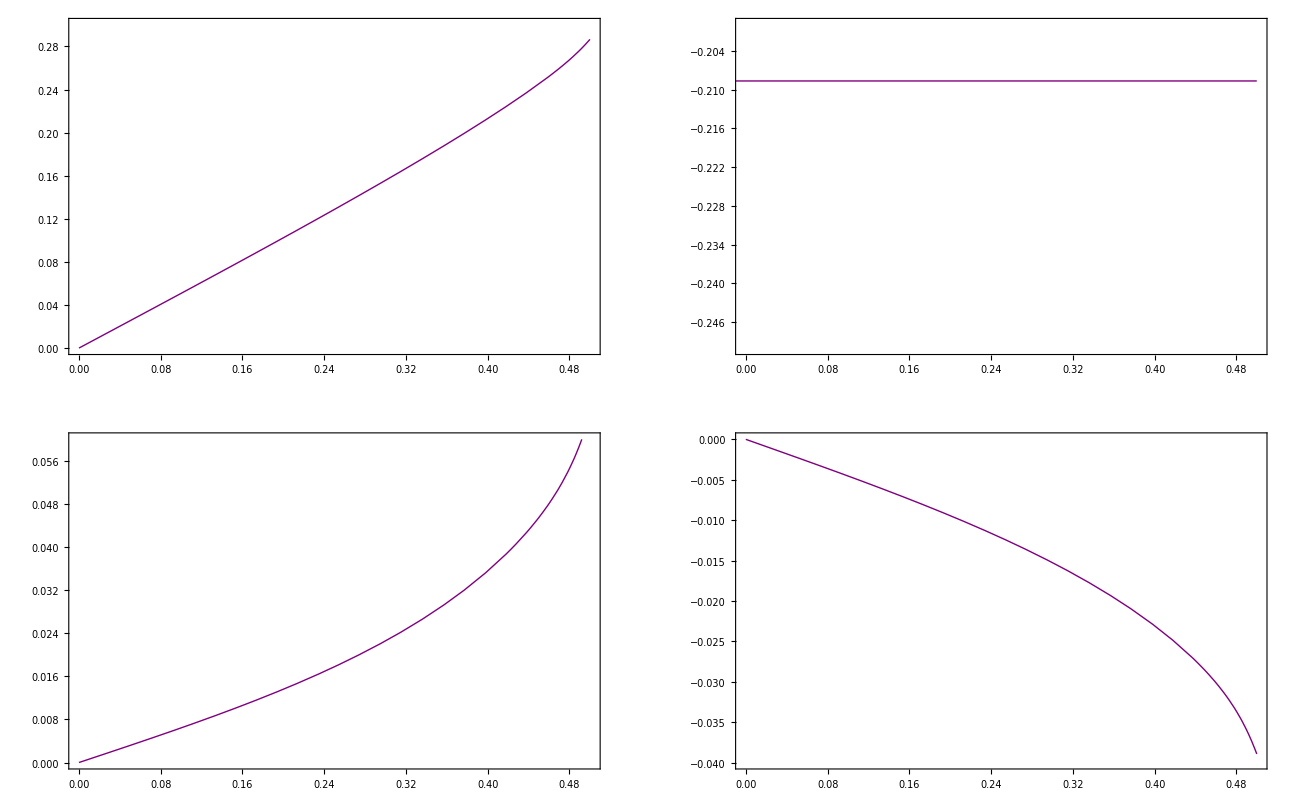

```mathematica
show={2,3,4,5};
style={{Red},{Blue},{Green},{Purple}};
xa=-0.5;
xe=0.5;
vxNSF[x_]=0.44379076287665603 x;

GraphicsGrid[{{
Plot[Evaluate[Map[vxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,0.3}},PlotStyle->style],
Plot[Evaluate[Map[σxyN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.25,-0.2}},PlotStyle->style]},
{Plot[Evaluate[Map[vxN[#][x]-vxNSF[x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.0,0.06}},PlotStyle->style],Plot[Evaluate[Map[qxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.04,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,vxN[nr][##],σxyN[nr][##],qxN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p5_nst300_Nc150_cMax5p0.dat,110913]

## Poiseuille Flow

```mathematica
SetDirectory["/home/torrilhon/Documents/RWTH/Projects/KineticReference/BGKPoiseuilleFlow"]
SetDirectory["C:/Users/mt/Science/Projekte/KineticReference/BGKPoiseuilleFlow"]
```

/home/torrilhon/Documents/RWTH/Projects/KineticReference/BGKPoiseuilleFlow

SetDirectory::cdir: Cannot set current directory to "C:/Users/mt/Science/Projekte/KineticReference/BGKPoiseuilleFlow".

$Failed

### Kn = 0.1

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
nr=2;

tau=0.1;
setup={vWL->0.0,vWR->0.0};
rhs=Flatten[Table[ffM[0,1,0,0],{i,1,nn}]];

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
time=AbsoluteTiming[
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]-rhs];
]⟦1⟧;
Print["system size: ",nn Nf Nc," linear solve - time: ",time];

xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

vxN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
σxyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
qxN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
```

system size: 45000 linear solve - time: 5.74548

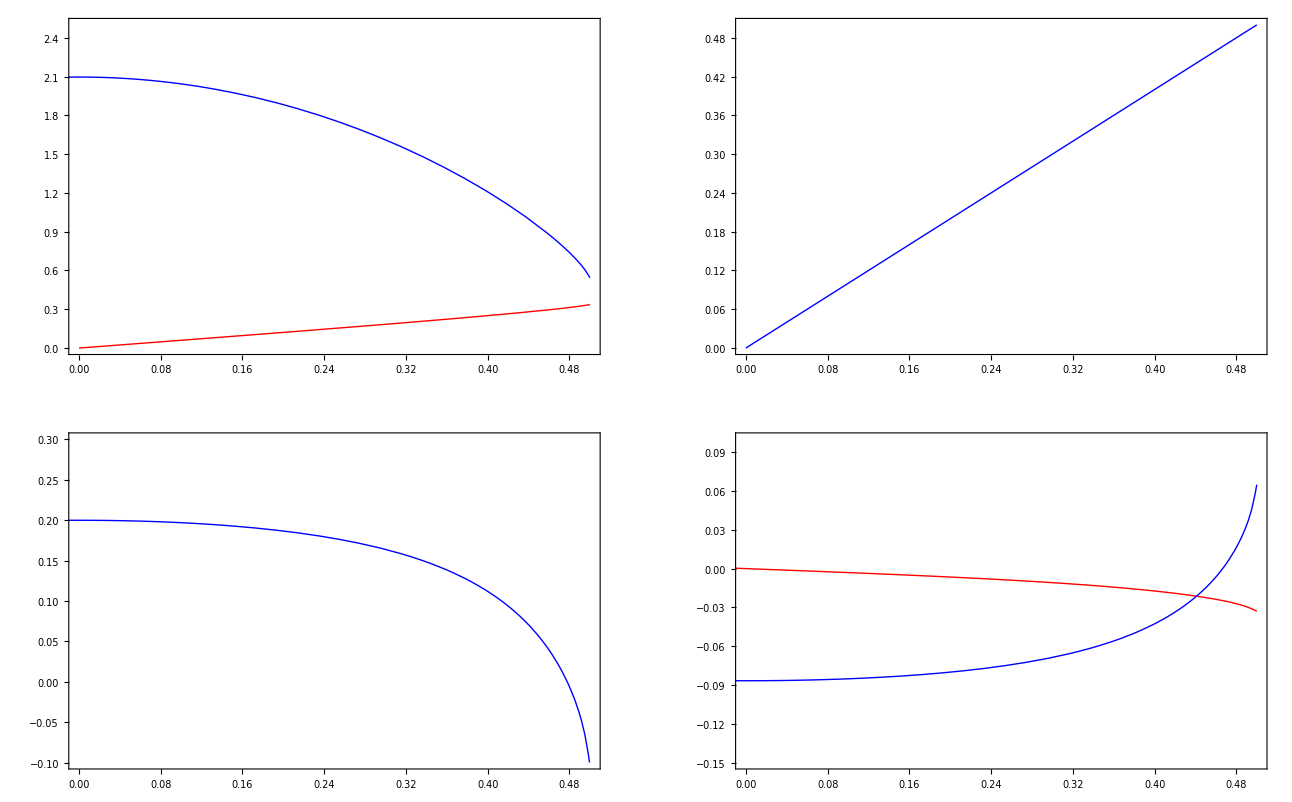

```mathematica
show={1,2};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
vxNSF[x_]=1.89665706865775-5. x^2;

GraphicsGrid[{{
Plot[Evaluate[Map[vxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,2.5}},PlotStyle->style],
Plot[Evaluate[Map[σxyN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0,0.5}},PlotStyle->style]},
{Plot[Evaluate[Map[vxN[#][x]-vxNSF[x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.1,0.3}},PlotStyle->style],Plot[Evaluate[Map[qxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.15,0.1}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,vxN[nr][##],σxyN[nr][##],qxN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p1_nst300_Nc150_cMax5p0.dat,115748]

### Kn = 0.3

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
nr=2;

tau=0.3;
setup={vWL->0.0,vWR->0.0};
rhs=Flatten[Table[ffM[0,1,0,0],{i,1,nn}]];

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
time=AbsoluteTiming[
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]-rhs];
]⟦1⟧;
Print["system size: ",nn Nf Nc," linear solve - time: ",time];

xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

vxN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
σxyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
qxN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
```

system size: 45000 linear solve - time: 5.71371

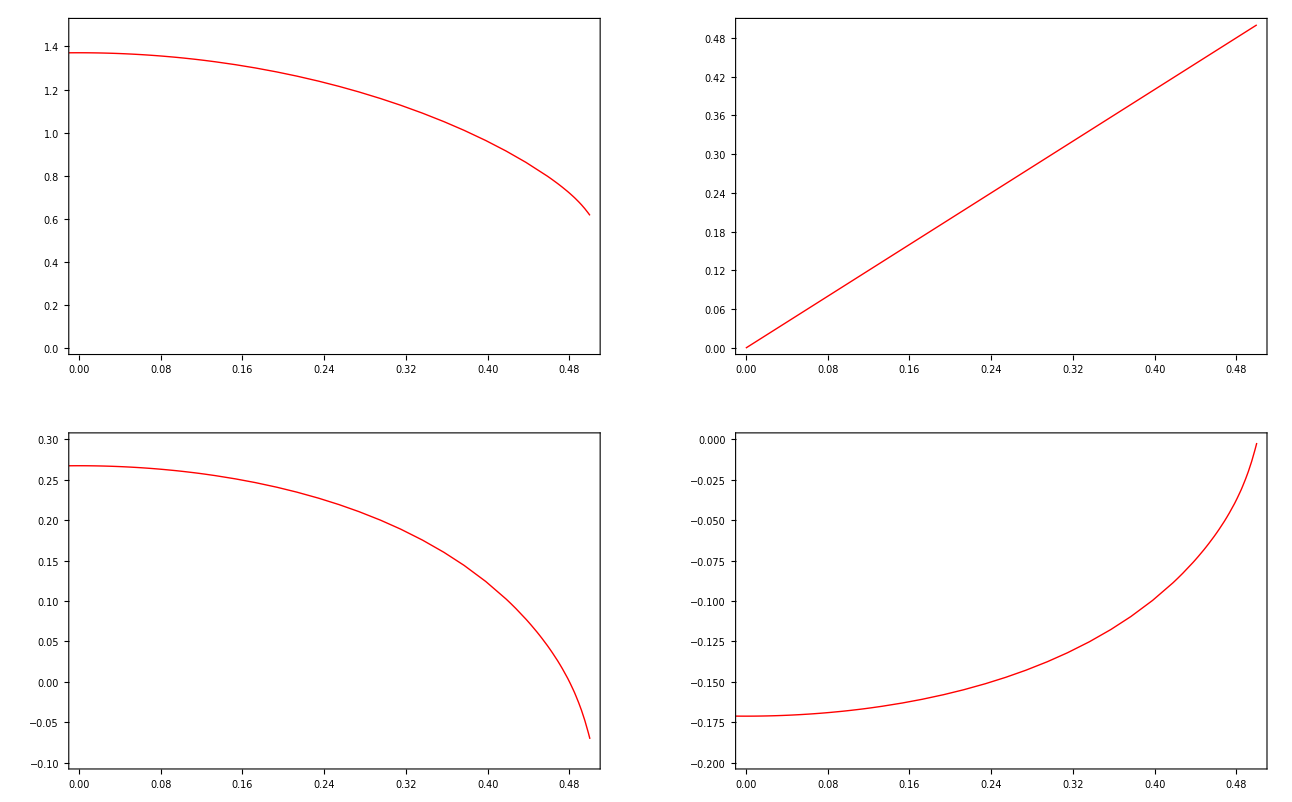

```mathematica
show={2};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
vxNSF[x_]=1.1033237353244167-1.6666666666666667 x^2;

GraphicsGrid[{{
Plot[Evaluate[Map[vxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,1.5}},PlotStyle->style],
Plot[Evaluate[Map[σxyN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0,0.5}},PlotStyle->style]},
{Plot[Evaluate[Map[vxN[#][x]-vxNSF[x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.1,0.3}},PlotStyle->style],Plot[Evaluate[Map[qxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.2,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,vxN[nr][##],σxyN[nr][##],qxN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p3_nst300_Nc150_cMax5p0.dat,121109]

### Kn = 0.5

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
nr=2;

tau=0.5;
setup={vWL->0.0,vWR->0.0};
rhs=Flatten[Table[ffM[0,1,0,0],{i,1,nn}]];

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
time=AbsoluteTiming[
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]-rhs];
]⟦1⟧;
Print["system size: ",nn Nf Nc," linear solve - time: ",time];

xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

vxN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
σxyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
qxN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
```

system size: 45000 linear solve - time: 5.88415

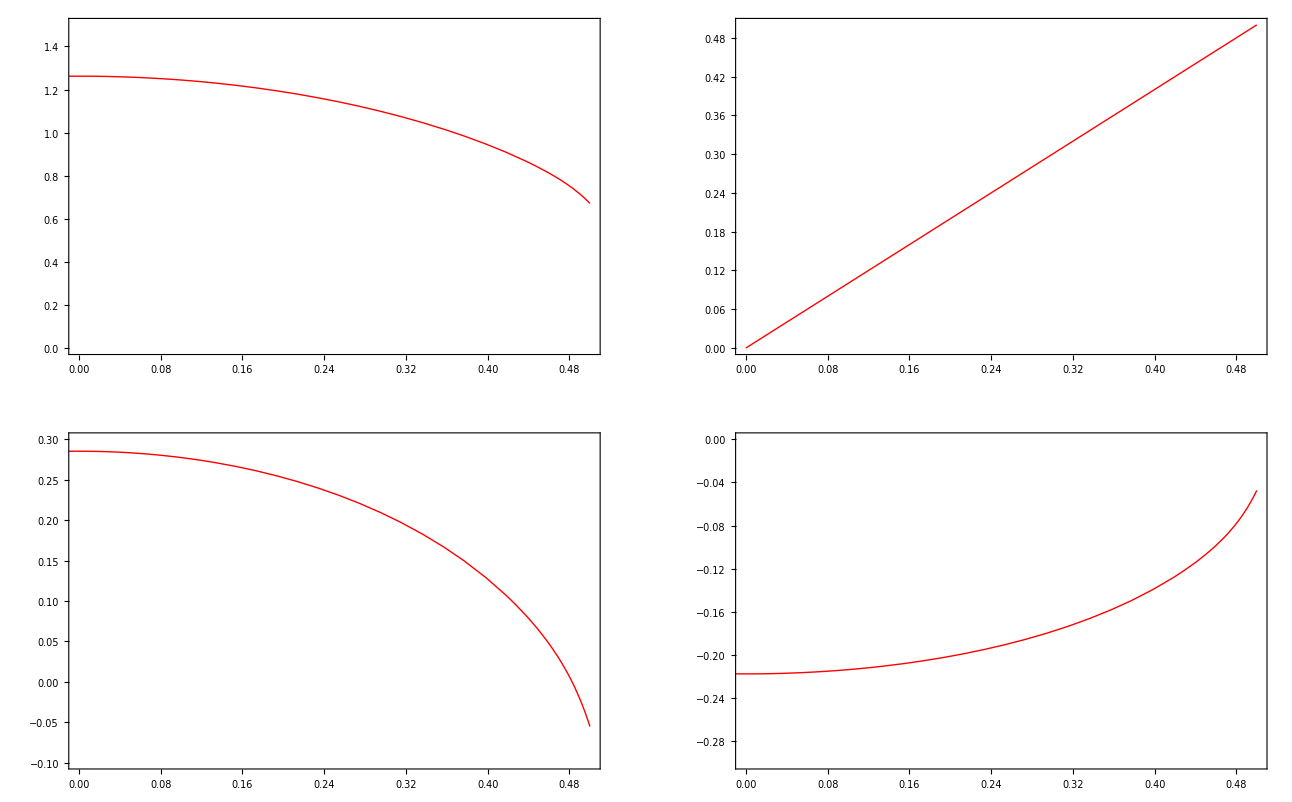

```mathematica
show={2};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
vxNSF[x_]=0.97665706865775-1. x^2;

GraphicsGrid[{{
Plot[Evaluate[Map[vxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0.0,1.5}},PlotStyle->style],
Plot[Evaluate[Map[σxyN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{0,0.5}},PlotStyle->style]},
{Plot[Evaluate[Map[vxN[#][x]-vxNSF[x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.1,0.3}},PlotStyle->style],Plot[Evaluate[Map[qxN[#][x]&,show]],{x,-1/2,1/2},PlotRange->{{0,1/2},{-0.3,0.0}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGKreduced",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,vxN[nr][##],σxyN[nr][##],qxN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGKreduced_tau0p5_nst300_Nc150_cMax5p0.dat,126402]

## BGK discretization (1 distributions, normal)

```mathematica
Clear[Maxwell,ρ,vx,vy,θ,fM0,fM,Nc,Nf,nn,cMax,dcx,dcy,cxPos,cyPos,fM$,cons,cons1,Maxwell,ffM]

fM[Cy_,ρ_,vx_,vy_,θ_]:={ρ+vy Cy+θ/2(Cy^2-1)}1/(√(2π))Exp[-Cy^2/2];
proj[Cy_]:={{1},{Cy},{(Cy^2-1)},{Cy(Cy^2-3)}};

ffM[ρ_,vx_,vy_,θ_]:=Maxwell.{ρ,vy,θ};

GetHalf[fin_,ii_]:=Take[Partition[fin,Nc]⟦Abs[ii]⟧,Sign[ii]Nc/2];

BoundaryDistribution[input_,side_,flag_]:=Block[{res,inL,inR},
Which[side=="L",
inL=Take[input,Nc/2];
res=Join[inL,GetHalf[ffM[ρL,0,0,θL],-flag]],
side=="R",
inR=Take[input,-Nc/2];
res=Join[GetHalf[ffM[ρR,0,0,θR],flag],inR]
];
res
];

BoundaryDistributionFull[input_,side_]:=Table[BoundaryDistribution[input⟦ii⟧,side,ii],{ii,1,Nf}]
```

```mathematica
Clear[n,dx,a,τ,uL,uR]
EqnP[n_,dx_,a_,τ_,uL_]:=Block[{ii,eqn1,eqn2,eqnN},
eqn1=a(uL-(u[1]+1/6(u[2]+3u[1]-4uL)))/dx-1/τ u[1];
eqn2=a(u[1]+1/6(u[2]+3u[1]-4uL)-(u[2]+1/4(u[3]-u[1])))/dx-1/τ u[2];
eqnN=a(u[n-1]+1/4(u[n]-u[n-2])-(u[n]+1/2(u[n]-u[n-1])))/dx-1/τ u[n];
Join[{eqn1,eqn2},
Table[a(u[i-1]+1/4(u[i]-u[i-2])-(u[i]+1/4(u[i+1]-u[i-1])))/dx-1/τ u[i],{i,3,n-1}],
{eqnN}]

];
EqnM[n_,dx_,a_,τ_,uR_]:=Block[{ii,eqnN,eqnN1,eqn1},
eqnN=a(u[n]-1/6(-u[n-1]-3u[n]+4uR)-uR)/dx-1/τ u[n];
eqnN1=a(u[n-1]-1/4(u[n]-u[n-2])-(u[n]-1/6(-u[n-1]-3u[n]+4uR)))/dx-1/τ u[n-1];
eqn1=a(u[1]-1/2(u[2]-u[1])-(u[2]-1/4(u[3]-u[1])))/dx-1/τ u[1];
Join[{eqn1},
Table[a(u[i]-1/4(u[i+1]-u[i-1])-(u[i+1]-1/4(u[i+2]-u[i])))/dx-1/τ u[i],{i,2,n-2}],
{eqnN1,eqnN}]

];
```

```mathematica
Clear[ρ,vx,vy,θ]
Clear[aP,aM,uR,uL,u,a]

nn=300;
Δx=1./nn;

Nf=1;
Nc=20;
cMax=5.;
dcy=2 cMax/(Nc-1);
cyPos=Table[-cMax+(j-1)dcy,{j,1,Nc}];


fM$={
Flatten[Transpose[Table[fM[cyPos⟦m⟧,1,0,0,0],{m,1,Nc}]]],
Flatten[Transpose[Table[fM[cyPos⟦m⟧,0,0,1,0],{m,1,Nc}]]],
Flatten[Transpose[Table[fM[cyPos⟦m⟧,0,0,0,1],{m,1,Nc}]]]};

cons=Normal[CoefficientArrays[Sum[proj[cyPos⟦j⟧].Table[u[j,ii],{ii,1,Nf}],{j,1,Nc}]dcy,Flatten[Table[Table[u[m,ii],{m,1,Nc}],{ii,1,Nf}]]]⟦2⟧];

Maxwell=Transpose[fM$]+Transpose[cons].Inverse[Normal[cons.Transpose[cons]]].(IdentityMatrix[4]⟦All,1;;3⟧-cons.Transpose[fM$]);

P=Maxwell.cons⟦1;;3⟧;

time=AbsoluteTiming[ (* direct initialization using compressed format !! *)
PP=SparseArray[Automatic,{nn Nf Nc,nn Nf Nc},0,{1,
{Table[i Nf Nc,{i,0,nn Nf Nc}],
Flatten[Table[Table[{i Nf Nc+m2},{m1,1,Nf Nc},{m2,1,Nf Nc}],{i,0,nn-1}],2]},
Flatten[Table[P,{i,1,nn}]]
}]
]⟦1⟧;
Print[" collision part - time: ",time];


{bcP,AdvP}=CoefficientArrays[EqnP[nn,Δx,aP,∞,uL],Table[u[i],{i,1,nn}]];
{bcM,AdvM}=CoefficientArrays[EqnM[nn,Δx,aM,∞,uR],Table[u[i],{i,1,nn}]];

time=AbsoluteTiming[
A=CoefficientArrays[Flatten[Transpose[Flatten[Table[{
Transpose[AdvM.Table[u[i,jj],{i,1,nn}]/.{aM u[i_,ii_]->Table[cyPos⟦m⟧u[i,m,ii],{m,1,Nc/2}]}],
Transpose[AdvP.Table[u[i,jj],{i,1,nn}]/.{aP u[i_,ii_]->Table[cyPos⟦m⟧u[i,m,ii],{m,Nc/2+1,Nc}]}]}
,{jj,1,Nf}],2]]]
,Flatten[Table[u[i,m,ii],{i,1,nn},{ii,1,Nf},{m,1,Nc}]]]⟦2⟧
]⟦1⟧;
Print[" advection part - time: ",time];


bc=Flatten[Table[Flatten[Table[{bcM⟦i⟧/.{uR->uR[ii]},bcP⟦i⟧/.{uL->uL[ii]}},{ii,1,Nf}]],{i,1,nn}]];

Do[
If[Length[bc⟦i⟧]==0,bc⟦i⟧=Table[0,{m,1,Nc/2}]]
,{i,1,Length[bc]}]

bc=bc/.{aP uL[ii_]->aP.uL[ii],aM uR[ii_]->aM.uR[ii]};
bc=bc/.{aP->DiagonalMatrix[Table[cyPos⟦m⟧,{m,Nc/2+1,Nc}]],aM->DiagonalMatrix[Table[cyPos⟦m⟧,{m,1,Nc/2}]]};
bc=Flatten[bc/.{uL[ii_]:>GetHalf[ffM[ρL,0,0,θL],-ii],uR[ii_]:>GetHalf[ffM[ρR,0,0,θR],ii]}];
```

collision part - time: 0.55136

advection part - time: 0.52535

## Simple Heat Conduction

```mathematica
SetDirectory["/home/torrilhon/Documents/RWTH/Projects/KineticReference"]
SetDirectory["C:/Users/mt/Science/Projekte/KineticReference"]
```

SetDirectory::cdir: Cannot set current directory to "/home/torrilhon/Documents/RWTH/Projects/KineticReference".

$Failed

C:\Users\mt\Science\Projekte\KineticReference

### Kn = 0.1

```mathematica
Clear[rho,ρN,vyN,θN,σyyN,qyN]
```

```mathematica
{nr,Nc,nn,rho}
{1,200,50,0.8794401898588436}
{2,200,100,0.8795132348662098}
{3,300,100,0.8795134728030819}
{4,300,150,0.8795262920058148}
```

```mathematica
nr=5;

tau=0.1;
rho[nr]=0.8787544170261329;
setup={ρL->-rho[nr],ρR->rho[nr],θL->1.0,θR->-1.0};

id=SparseArray[{i_,i_}->1,{Nf nn Nc,Nf nn Nc}];
xf=LinearSolve[A-1/tau(id-PP),Flatten[-bc/.setup]];
xf=ArrayReshape[xf,{nn,Nf,Nc}];

fbcL=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦1⟧-1/2 xf⟦All,All⟧⟦2⟧,"L"]/.setup];
fbcR=Flatten[BoundaryDistributionFull[3/2 xf⟦All,All⟧⟦nn⟧-1/2 xf⟦All,All⟧⟦nn-1⟧,"R"]/.setup];
uN=Join[{Flatten[{-0.5,cons.fbcL}]},Table[Flatten[{-0.5+Δx/2+(i-1)Δx,cons.Flatten[xf⟦All,All⟧⟦i⟧]}],{i,1,nn}],{Flatten[{0.5,cons.fbcR}]}];

{rho[nr],Total[uN⟦All,3⟧]}

ρN[nr]=Interpolation[uN⟦All,{1,2}⟧,InterpolationOrder->1];
vyN[nr]=Interpolation[uN⟦All,{1,3}⟧,InterpolationOrder->1];
θN[nr]=Interpolation[uN⟦All,{1,4}⟧,InterpolationOrder->1];
qyN[nr]=Interpolation[uN⟦All,{1,5}⟧,InterpolationOrder->1];
```

{0.878754,1.5632×10^-14}

```mathematica
p1={0.8807088926335978,-0.3906225784030601};
p2={0.9,-4.246153990989175};
p1⟦1⟧-p1⟦2⟧(p2⟦1⟧-p1⟦1⟧)/(p2⟦2⟧-p1⟦2⟧)
```

0.878754

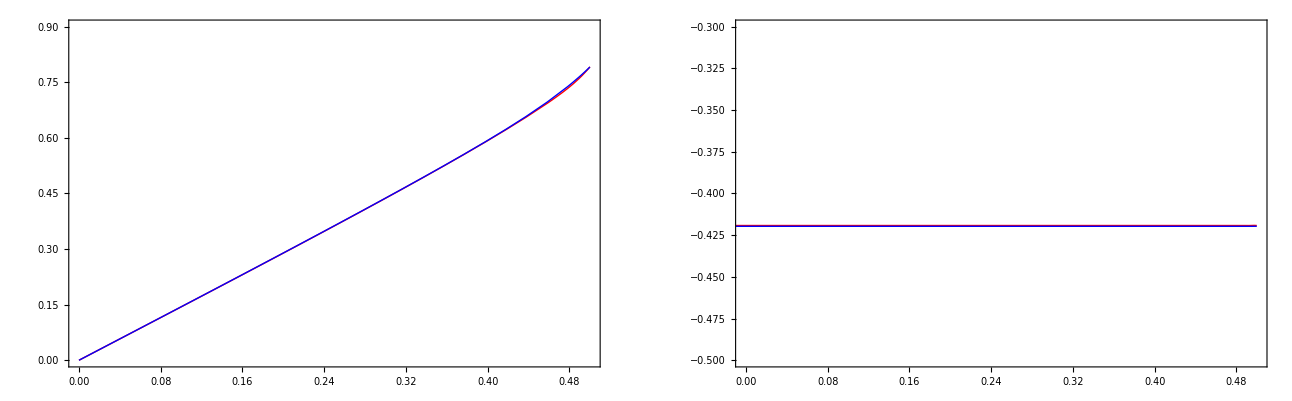

```mathematica
show={1,5};
style={{Red},{Blue},{Green}};
xa=-0.5;
xe=0.5;
θNSF[x_]=1.5228482041791787 x;

GraphicsGrid[{
{Plot[Evaluate[Map[θN[#][-x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{0.0,0.9}},PlotStyle->style],
Plot[Evaluate[Map[-qyN[#][x]&,show]],{x,xa,xe},PlotRange->{{0,1/2},{-0.5,-0.3}},PlotStyle->style]}}]
```

```mathematica
fp = OpenWrite[Filename["BGK1DSimpleHeat",tau,nn,Nc,cMax],FormatType->OutputForm,PageWidth->Infinity]
list=Map[N[{##,ρN[nr][##],vyN[nr][##],θN[nr][##],ρN[nr][##]+θN[nr][##],qyN[nr][##]},9]&,Join[{-0.5},Table[-0.5+Δx/2+(i-1)Δx,{i,1,nn}],{0.5}]];
Write[fp,MyFormat[TableForm[N[list,13],TableSpacing->{0,4}]]];
Close[fp];
```

OutputStream[Result_BGK1DSimpleHeat_tau0p1_nst200_Nc100_cMax5p0.dat,7365]